# AlternatingTreeGraph

Construct an alternating tree graph

## Definition

```mathematica
AlternatingTreeGraph[n_,options:OptionsPattern[Graph]]:=Module[{pathgraph,top,bottom},
pathgraph=PathGraph[Range[n]];top=UndirectedEdge@@@Transpose[{Range[2,n-1],Range[n+1,2 n-2]}];bottom=UndirectedEdge@@@Transpose[{Range[2,n-1],Range[2 n-1,3 n-4]}];IndexGraph[EdgeAdd[pathgraph,Join[top,bottom],options,GraphLayout->"SpringElectricalEmbedding"]]]
```

## Documentation

### Usage

AlternatingTreeGraph[n]

generates an alternating tree graph from a path graph withn vertices.

### Details & Options

An alternating tree J is a tree each of whose edges joins an inner vertex to an outer vertex so that each inner vertex of J meets exactly two edges of J.

An alternating tree graph has 3n-4 vertices.

AlternatingTreeGraph takes the same options as Graph.

## Examples

### Basic Examples

Make an alternating tree graph from the path graph with 10 vertices:

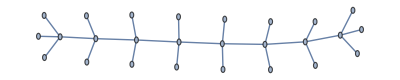

```mathematica
AlternatingTreeGraph[10]
```

### Scope

Create a large alternating tree graph:

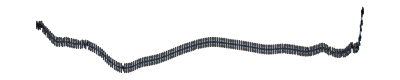

```mathematica
AlternatingTreeGraph[200]
```

### Options

#### GraphLayout

All graph layouts can be selected:

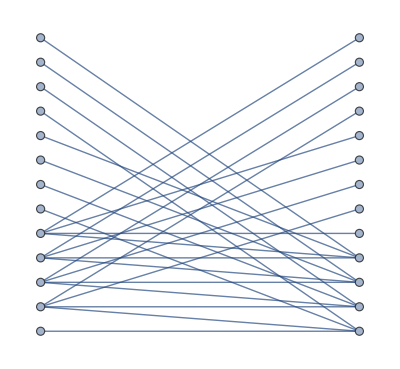
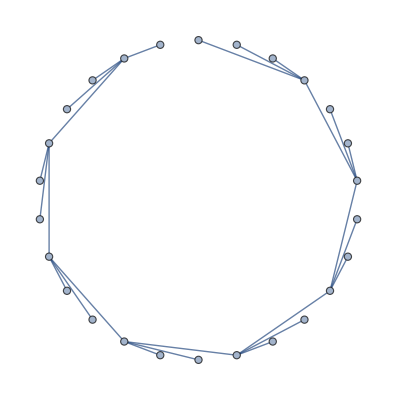
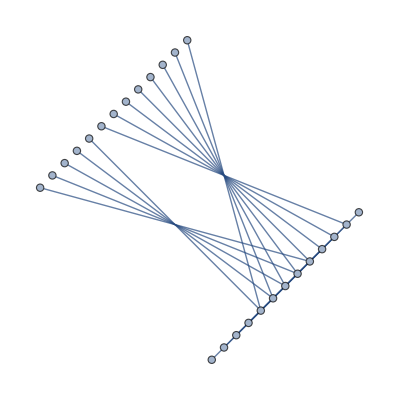
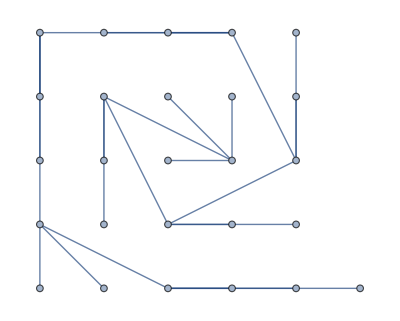
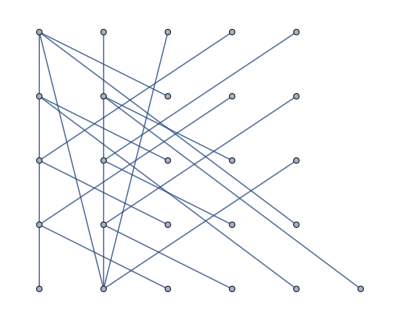
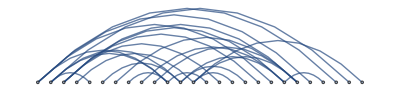
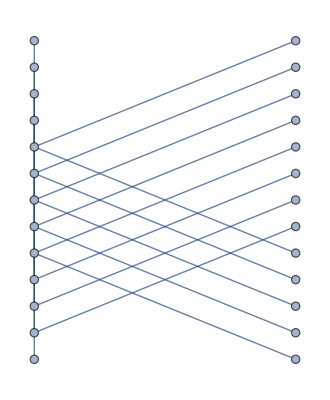
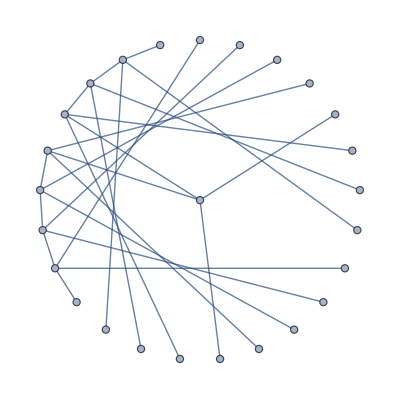
{-Graphics-BipartiteEmbedding,-Graphics-CircularEmbedding,-Graphics-CircularMultipartiteEmbedding,-Graphics-DiscreteSpiralEmbedding,-Graphics-GridEmbedding,-Graphics-LinearEmbedding,-Graphics-MultipartiteEmbedding,-Graphics-StarEmbedding,-Graphics-BalloonEmbedding,-Graphics-RadialEmbedding,-Graphics-LayeredEmbedding,-Graphics-GravityEmbedding,-Graphics-HighDimensionalEmbedding,-Graphics-SpectralEmbedding,-Graphics-SphericalEmbedding,-Graphics-SpringElectricalEmbedding,-Graphics-SpringEmbedding,-Graphics-TutteEmbedding}

```mathematica
Table[Labeled[AlternatingTreeGraph[10,GraphLayout->embedding],embedding],{embedding,{"BipartiteEmbedding","CircularEmbedding","CircularMultipartiteEmbedding","DiscreteSpiralEmbedding","GridEmbedding","LinearEmbedding","MultipartiteEmbedding","StarEmbedding","BalloonEmbedding","RadialEmbedding","LayeredEmbedding","GravityEmbedding","HighDimensionalEmbedding","SpectralEmbedding","SphericalEmbedding","SpringElectricalEmbedding","SpringEmbedding","TutteEmbedding"}}]
```

Try SpringEmbedding if SpringElectricalEmbedding does not work well:

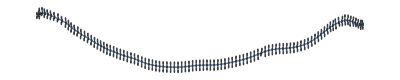

```mathematica
AlternatingTreeGraph[100]
```

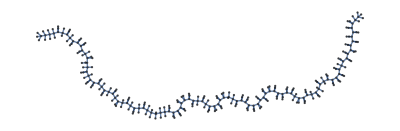

```mathematica
AlternatingTreeGraph[100,GraphLayout->"SpringEmbedding"]
```

### Applications

Find the graph center and graph periphery:

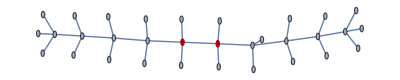

```mathematica
HighlightGraph[AlternatingTreeGraph[12],GraphCenter[AlternatingTreeGraph[12]]]
```

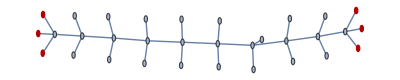

```mathematica
HighlightGraph[AlternatingTreeGraph[12],GraphPeriphery[AlternatingTreeGraph[12]]]
```

### Properties and Relations

Use FindSequenceFunction to find a pattern in the order and size of the graph:

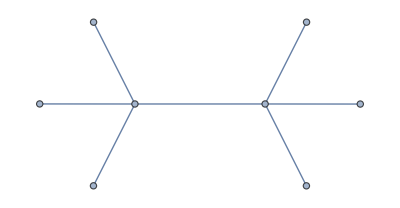
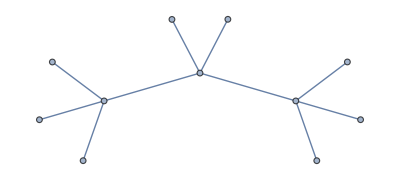
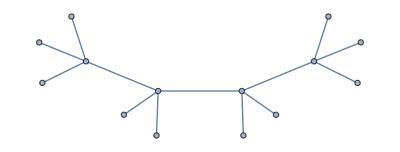
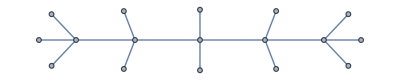
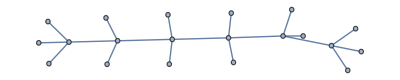
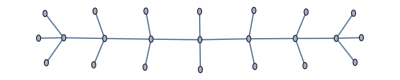
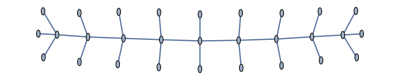
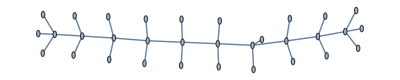
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
graphs=AlternatingTreeGraph/@Range[4,20]
```

```mathematica
FindSequenceFunction[VertexCount/@graphs]
```

5+3 #1&

```mathematica
FindSequenceFunction[EdgeCount/@graphs]
```

4+3 #1&

Predict the size of a 2980 length alternating tree:

```mathematica
graphs=AlternatingTreeGraph/@Range[4,20]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
FindSequenceFunction[VertexCount/@graphs][2980]
```

8945

```mathematica
FindSequenceFunction[EdgeCount/@graphs][2980]
```

8944

## Source & Additional Information

### Contributed By

Peter Burbery

### Keywords

trees

graphs

blossom inequalities

arc routing

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Repository Tools
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction
 Wolfram Physics Project |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Just For Fun
 Machine Learning
 Programming Utilities
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics

### Related Symbols

PathGraph

TreeGraph

Tree

### Related Resource Objects

HexagonalGridGraph

TriangularGridGraph

### Source/Reference Citation

Edmonds J., "Paths, Trees, and Flowers." Canadian Journal of Mathematics, vol. 17, 449-467, 1965.
DOI: 10.4153/CJM-1965-045-4

### Links

Link to other related material

### Tests

```mathematica
MyFunction[x,y]
```

x y

### Compatibility

#### Wolfram Language Version

12.3+

#### Operating System

Windows |  Mac |  Unix

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

## Author Notes

Additional information about limitations, issues, etc.

## Submission Notes

Additional information for the reviewer.